```mathematica
Integrate[A (Sin[B x])^2,x]
```

A (x/2-Sin[2 B x]/(4 B))

```mathematica
At = A (Cos[B (x-π/(2 B))])^2
```

A Cos[B (-π/(2 B)+x)]^2

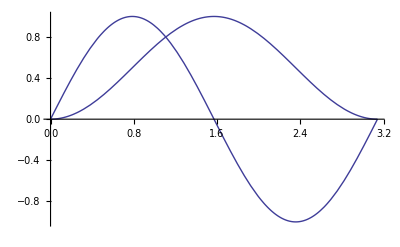

```mathematica
Plot[{At, DAT} /. {A->1,B->1,C->0}, {x,0, 2 π /2}]
```

```mathematica
Integrate[At,{x, -π/(2 B)+C,  π/(2B)+C}]
```

(A π)/(2 B)

```mathematica
Solve[At == 0]
```

{{A→0},{Cos[B (-C+x)]→0},{Cos[B (-C+x)]→0}}

```mathematica
DAT = D[At,{x,1}]
```

-2 A B Cos[B (-π/(2 B)+x)] Sin[B (-π/(2 B)+x)]

```mathematica
DAT/.{x->π/(4 B)}
```

A B

```mathematica
Solve[Cos[x]==Sin[x], x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-(3 π)/4},{x→π/4}}

```mathematica
Cos[π/4]
```

1/(√2)

```mathematica
IAt = Integrate[At,x] - (Integrate[At, x]/.{x->-π/(2 B)})
```

(A π)/(4 B)+A (x/2+Sin[2 B x]/(4 B))

```mathematica
IIAt = Integrate[IAt + Z , x] - (Integrate[IAt + Z, x]/.{x->-π/(2 B)})
```

-A/(8 B^2)+(A π^2)/(16 B^2)+(A π x)/(4 B)+(A x^2)/4+(π Z)/(2 B)+x Z-(A Cos[2 B x])/(8 B^2)

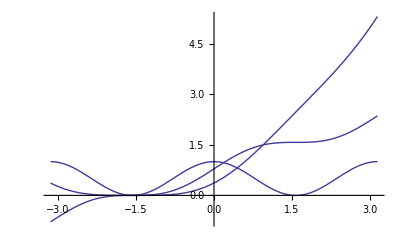

```mathematica
Plot[{At,IAt, IIAt}/.{A->1,B->1,C->0,Z->0},{x,-π,π
}]
```

```mathematica
Simplify[IIAt]
```

(A (-2+π^2+4 B π x+4 B^2 x^2)+8 B (π+2 B x) Z-2 A Cos[2 B x])/(16 B^2)

```mathematica
IAt/.x->(-π/(2 B))
```

A (1/2 (-C-π/(2 B))+Sin[2 B (-C-π/(2 B))]/(4 B))

```mathematica
Simplify[IAt]
```

(A (-2 B C+π+2 B x+Sin[2 B (-C+x)]))/(4 B)